```mathematica
(*Mathematica*)
```

```mathematica
Clear[t,a,p,aa,bb]
```

```mathematica
(* 7 star cycle7 Heptagon *)
```

```mathematica
n0=7
```

7

```mathematica
(* substitution *)
```

```mathematica
s[1]={4,2,6,0,0,0,0,0,0}; s[2]={5,3,7,0,0,0,0,0,0}; s[3]={6,4,1,0,0,0,0,0,0,0}; s[4]={7,5,2,0,0,0,0,0,0,0,0};s[5]={1,6,3,0,0,0,0,0,0,0,0};
s[6]={2,7,4,0,0,0,0,0,0,0,0};
s[7]={3,1,5,0,0,0,0,0,0,0,0};
```

```mathematica
(* make matrix*)
```

```mathematica
M=Table[Table[Count[s[j],i],{i,1,n0}],{j,1,n0}]
```

{{0,1,0,1,0,1,0},{0,0,1,0,1,0,1},{1,0,0,1,0,1,0},{0,1,0,0,1,0,1},{1,0,1,0,0,1,0},{0,1,0,1,0,0,1},{1,0,1,0,1,0,0}}

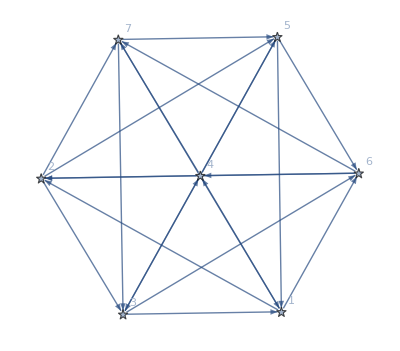

```mathematica
AdjacencyGraph[M,VertexLabels->"Name",ImageSize->Full,VertexShapeFunction->"Star"]
```

```mathematica
(* make polynomial*)
```

```mathematica
Det[M-x*IdentityMatrix[n0]]
```

3+14 x+28 x^2+28 x^3+14 x^4-x^7

```mathematica
x/.NSolve[CharacteristicPolynomial[M,x]==0,x]
```

{-0.5-2.19064 ⅈ,-0.5+2.19064 ⅈ,-0.5-0.240787 ⅈ,-0.5+0.240787 ⅈ,-0.5-0.62698 ⅈ,-0.5+0.62698 ⅈ,3.}

```mathematica
Abs[%]
```

{2.24698,2.24698,0.554958,0.554958,0.801938,0.801938,3.}

```mathematica
Clear[s,p]
```

```mathematica
(* program to express the substitution *)
```

```mathematica
Clear[s,t,p]
```

```mathematica
s[1]={4,2,6}; s[2]={5,3,7}; s[3]={6,4,1}; s[4]={7,5,2};s[5]={1,6,3};
s[6]={2,7,4};
s[7]={3,1,5};
```

```mathematica
t[a_] :=Flatten[s/@a];
```

```mathematica
w=Flatten[Table[s[i],{i,7}]]
```

{4,2,6,5,3,7,6,4,1,7,5,2,1,6,3,2,7,4,3,1,5}

```mathematica
p[0]=w;p[1]=t[p[0]];
```

```mathematica
p[n_]:=t[p[n-1]]
```

```mathematica
aa=p[10];
```

```mathematica
Length[aa]
```

1240029

```mathematica
(* graphing subroutine*)
```

```mathematica
v=Table[N[{Cos[2*Pi*i/7],Sin[2*Pi*i/7]}],{i,7}]
```

{{0.62349,0.781831},{-0.222521,0.974928},{-0.900969,0.433884},{-0.900969,-0.433884},{-0.222521,-0.974928},{0.62349,-0.781831},{1.,0.}}

```mathematica
bb=aa/. 1->v[[1]]/. 2->v[[2]]/. 3->v[[3]]/. 4->v[[4]]/. 5->v[[5]]/. 6->v[[6]]/. 7->v[[7]];
```

```mathematica
cc=FoldList[Plus,{0,0},bb];
```

```mathematica
g0=ListPlot[cc,PlotRange->All,Axes->False,ImageSize->{2000,2000},PlotStyle->{PointSize[0.001]},ColorFunction->Hue];
```

```mathematica
allColors=ColorData["Legacy"][[3,1]];
firstCols={"White","AliceBlue","LightBlue" ,"Cyan","ManganeseBlue","DodgerBlue" ,"Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow", "Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow", "Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow", "Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
dd=Flatten[ParallelTable[{PointSize[0.001],cols[[aa[[n]]]],Point[cc[[n]]]},{n,Min[Length[cc],Length[aa]]}]];
```

```mathematica
g1=Show[Graphics[dd],ImageSize->{2000,2000},Background->Black];
```

```mathematica
Export["7Symbol_cycle7_Heptagon9thkind_level10_StartVector.jpg",GraphicsGrid[{{g0},{g1}},ImageSize->{2000,4000}]]
```

7Symbol_cycle7_Heptagon9thkind_level10_StartVector.jpg

```mathematica
(*end*)
```